## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
lambdamin=400; (*nm*)
lambdamax=700;(*nm*)
radiomin=10; (*nm*)
radiomax=100; (*nm*)
refractiveindexAire=1;
refractiveindexAgua=1.33;
energyTicksMajor={1.8,1.9,2.1,2.3,2.5,2.8,3.1};
energyTicksMinor={3.5,4.2,4.6,6,8,9,12,40};
radios=Range[10,100,22];
lambdas=Range[lambdamin,lambdamax,10];
refractiveindexes=Range[1,2,0.01];
```

El programa de a continuación está diseñado para ingresar arreglos de datos experimentales

```mathematica
(*Se definen las funciones de Riccati-Bessel y sus correspondientes diferenciales *)
```

```mathematica
ψn[n_,x_]:= x*SphericalBesselJ[n,x]
ξn[n_,x_]:=x*SphericalHankelH1[n,x]
dψn[n_,x_]:=-n *SphericalBesselJ[n,x]+ x * SphericalBesselJ[n-1,x] 
dξn[n_,x_]:=-n * SphericalHankelH1[n,x] + x* SphericalHankelH1[n-1,x]
```

### Definición de funciones

```mathematica
(* Se define el criterio de Wiscombe y se emplea la siguiente notación:
- nm -> Índice de refracción del medio en el que está inmersa la nanopartícula
- a -> Radio de la nanopartícula
- lambda -> Longitud de onda de interés
- n -> multipolo a considerar
*)
```

```mathematica
criterioWiscombe[nm_,a_,lambda_]:=Module[{x,Wiscombe},
						x=(2 Pi nm a)/lambda;							
						Wiscombe=Round[x+ 4*x^(1/3)+2];
						Wiscombe]
```

```mathematica
(* Se definen los coeficientes de Mie y se emplea la siguiente notación:
- np -> Índice de refracción de la nanopartícula
- nm -> Índice de refracción del medio en el que está inmersa la nanopartícula
- a -> Radio de la nanopartícula
- lambda -> Longitud de onda de interés
- n -> multipolo a considerar
*)
```

```mathematica
mieCoefAn[np_,nm_,a_,lambda_,n_]:=Module[{m,x,an},
						m=np/nm;
						x=(2 Pi nm a)/lambda;							
						an=((m ψn[n,m x] dψn[n,x])-(ψn[n,x] dψn[n,m x]))/((m ψn[n,m x] dξn[n,x])-(ξn[n,x] dψn[n,m x])); 
						an]
```

```mathematica
mieCoefBn[np_,nm_,a_,lambda_,n_]:=Module[{m,x,bn},
						m=np/nm;
						x=(2 Pi nm a)/lambda;							
						bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
						bn]
```

```mathematica
(* Se definen las secciones transversales de esparcimiento, absorción y extinción con la siguiente notación
- np -> Índice de refracción de la nanopartícula
- nm -> Índice de refracción del medio en el que está inmersa la nanopartícula
- a -> Radio de la nanopartícula
- lambda -> Longitud de onda de interés
- nmax -> Sumar las contribucion es desde el dipolo hasta el nmax multipolo
Estas funciones regresan cuatro valores en su salida en el orden:
- an -> Modo eléctrico
- bn -> Modo magnético
- Csca/Cabs/Cext -> Sección transversal de esparcimiento/absorción/extinción
- Qsca/Qabs/Qext -> Eficiencia de esparcimiento/absorción/extinción
*)
```

```mathematica
mieQsca[np_,nm_,a_,lambda_]:=Module[{nmax,an,bn,k,Csca,Qsca},
nmax=criterioWiscombe[nm,a,lambda];
an=mieCoefAn[np,nm,a,lambda,#]&/@Range[1,nmax];
bn=mieCoefBn[np,nm,a,lambda,#]&/@Range[1,nmax];
Csca= (lambda^2 )/(2*π* Norm[nm]^2)*(Sum[(2 n +1)(Norm[an[[n]] ]^2+Norm[bn[[n]]] ^2),{n,nmax}]);
Qsca=Csca/(Pi* a^2) ;
{an,bn,Csca,Qsca}]
```

```mathematica
mieQext[np_,nm_,a_,lambda_]:=Module[{nmax,an,bn,Cext,Qext},
nmax=criterioWiscombe[nm,a,lambda];
an=mieCoefAn[np,nm,a,lambda,#]&/@Range[1,nmax];
bn=mieCoefBn[np,nm,a,lambda,#]&/@Range[1,nmax];
Cext=(lambda^2)/(2 Pi Norm[nm]^2)*Sum[(2 n+1) (Re[an[[n]]]+Re[bn[[n]]]),{n,1,nmax}];
Qext=Cext/(Pi a^2);
{an,bn,Cext,Qext}]
```

```mathematica
mieQabs[np_,nm_,a_,lambda_]:=mieQext[np,nm,a,lambda]-mieQsca[np,nm,a,lambda]
```

```mathematica
(* Función para graficar las 3 eficiencias con un solo radio*)
```

```mathematica
plotMieEfficiencies[qext_,qsca_,qabs_,energyTicksMajor_,radius_,lambdamin_,lambdamax_]:=Module[{majorTicks},(*Calcular ticks mayores en energía*)majorTicks=Module[{positions},positions=h c/#&/@energyTicksMajor;
Transpose[{positions,energyTicksMajor}]];
(*Graficar*)ListLinePlot[{qext,Style[qsca,Dashed,Red],qabs},Frame->True,FrameStyle->Directive[Black,FontFamily->"Arial",Magnification->1.4],FrameLabel->{{Row[Style[#,Magnification->1.6]&/@{Subscript["Q","ext"],Subscript["Q","abs"],Subscript["Q","sca"]},","],None},{Style["λ [nm]",Magnification->1.6],Style["ℏω [eV]",Magnification->1.6]}},LabelStyle->{FontFamily->"Arial",Black},FrameTicks->{{Automatic,None},{Automatic,majorTicks}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[Subscript["Q","ext"],Magnification->1.1],Style[Subscript["Q","sca"],Magnification->1.1],Style[Subscript["Q","abs"],Magnification->1.1]},LegendMarkerSize->{15,5},LegendMargins->0,LegendLayout->{"Column",1}],{0.85,0.75}],ImagePadding->{{70,10},{50,50}},PlotLabel->Style[Row[{"Radio ",radius," nm"}],FontFamily->"Arial",Magnification->1.5]]];
```

```mathematica
(* Función para graficar una eficiencia pero con varios radios*)
```

```mathematica
plotMieEfficiencie[qlist_,energyTicksMajor_,lambdamin_,lambdamax_,radios_]:=Module[{majorTicks},(*Calcular ticks mayores en energía*)majorTicks=Module[{positions},positions=h c/#&/@energyTicksMajor;
Transpose[{positions,energyTicksMajor}]];
(*Graficar*)ListLinePlot[qlist,Frame->True,FrameStyle->Directive[Black,FontFamily->"Arial",Magnification->1.4],FrameLabel->{{Row[Style[#,Magnification->1.6]&/@{Subscript["Q","ext"]}],None},{Style["λ [nm]",Magnification->1.6],Style["ℏω [eV]",Magnification->1.6]}},LabelStyle->{FontFamily->"Arial",Black},FrameTicks->{{Automatic,None},{Automatic,majorTicks}},PlotRange->All,PlotLegends->Placed[LineLegend[Table[Style["r = "<>ToString[r]<>" nm",Magnification->1.1],{r,radios}],LegendMarkerSize->{15,5},LegendMargins->0,LegendLayout->{"Column",1}],{0.85,0.55}],ImagePadding->{{70,10},{50,50}}
]
]
```

```mathematica
(* Función para hacer un mapa de intensidades de Qsca variando radio y longitud de onda*)
```

```mathematica
plotQDensity[qsca_]:=
ListDensityPlot[qsca,FrameLabel->{"λ [nm]","a [nm]"},ColorFunction->"SunsetColors",InterpolationOrder->1,Mesh->Automatic,Frame->True,FrameStyle->Directive[Black,FontFamily->"Arial",Magnification->1.4],ImagePadding->{{70,10},{50,30}},PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[Black,FontFamily->"Arial",Magnification->1.4],LegendLabel->Subscript["Q","sca"],LegendMarkerSize->200],{After,Top}]]
```

```mathematica
(* Función para hacer un mapa de intensidades de Qsca variando índice de refracción y longitud de onda*)
```

```mathematica
plotQDensityRI[qsca_]:=
ListDensityPlot[qsca,FrameLabel->{"λ [nm]"," RI"},ColorFunction->"SunsetColors",InterpolationOrder->1,Mesh->Automatic,Frame->True,FrameStyle->Directive[Black,FontFamily->"Arial",Magnification->1.4],ImagePadding->{{70,10},{50,30}},PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[Black,FontFamily->"Arial",Magnification->1.4],LegendLabel->Subscript["Q","sca"],LegendMarkerSize->200],{After,Top}]]
```

```mathematica
(* Función para hacer un mapa de intensidades de Qsca variando índice de refracción, longitud de onda y radio*)
```

```mathematica
plotQDensityRI3D[qsca_]:=
ListDensityPlot3D[qsca,ColorFunction->"SunsetColors",ImagePadding->{{70,10},{50,30}},PlotLegends->Automatic,PlotRange->All]
```

```mathematica
4*Pi/4.5
```

2.79253

## Vidrio

```mathematica
hola=mieQsca[1.5,1.33,4000,650][[3]]
holaAbs=mieQabs[1.5,1.33,4000,650][[3]]
```

9.89806×10^7

0.

```mathematica
(Abs[(1247776348.93765-hola)]/hola)*100
(Abs[(93161013.582019-hola)]/hola)*100
(Abs[(93125603.782360-hola)]/hola)*100
(Abs[(93344743.154767-hola)]/hola)*100
(Abs[(94536226.303384-hola)]/hola)*100
(Abs[(95983229.333652-hola)]/hola)*100
```

1160.63

5.87951

5.91528

5.69389

4.49013

3.02823

```mathematica
3.75/3.3
```

1.13636

```mathematica
gCabsMie=Table[{λ,mieQabs[1.5,1.33,4000,λ][[3]]},{λ,400,800,5}];
gCscaMie=Table[{λ,mieQsca[1.5,1.33,4000,λ][[3]]},{λ,400,800,40}];
gCextMie=Table[{λ,mieQext[1.5,1.33,4000,λ][[3]]},{λ,400,800,40}];
```

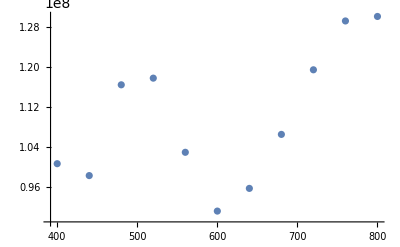

```mathematica
ListPlot[{gCscaMie}]
```

```mathematica
mieQext[1.5,1.33,4000,435][[3]]
```

9.72699×10^7

```mathematica
h c/1
```

1240.7

```mathematica
1.5^2
```

2.25

```mathematica
1.33^2
```

1.7689

```mathematica
h c/435
```

2.85218

```mathematica
gCextMie
```

{{400,4.38169×10^8},{405,4.3785×10^8},{410,4.30226×10^8},{415,4.21581×10^8},{420,4.11406×10^8},{425,4.01709×10^8},{430,3.94465×10^8},{435,3.91115×10^8},{440,3.92587×10^8},{445,3.99484×10^8},{450,4.12176×10^8},{455,4.21317×10^8},{460,4.27058×10^8},{465,4.35348×10^8},{470,4.43883×10^8},{475,4.40009×10^8},{480,4.42303×10^8},{485,4.33669×10^8},{490,4.25972×10^8},{495,4.18225×10^8},{500,4.0904×10^8},{505,3.99547×10^8},{510,4.02625×10^8},{515,3.89177×10^8},{520,3.90923×10^8},{525,3.94121×10^8},{530,3.94925×10^8},{535,4.02836×10^8},{540,4.16931×10^8},{545,4.19826×10^8},{550,4.25857×10^8},{555,4.3921×10^8},{560,4.40887×10^8},{565,4.49223×10^8},{570,4.49702×10^8},{575,4.49978×10^8},{580,4.47972×10^8},{585,4.44235×10^8},{590,4.3927×10^8},{595,4.33484×10^8},{600,4.27139×10^8},{605,4.20238×10^8},{610,4.12857×10^8},{615,4.05565×10^8},{620,3.99103×10^8},{625,3.93882×10^8},{630,3.89923×10^8},{635,3.87179×10^8},{640,3.85675×10^8},{645,3.86042×10^8},{650,3.94246×10^8},{655,3.90879×10^8},{660,4.01781×10^8},{665,4.00559×10^8},{670,4.05432×10^8},{675,4.11507×10^8},{680,4.23114×10^8},{685,4.31337×10^8},{690,4.32423×10^8},{695,4.37016×10^8},{700,4.48986×10^8}}

Datos obtenidos de Johnson & Christy  DOI: https://doi.org/10.1103/PhysRevB.6.4370

```mathematica
au=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau1=Drop[Drop[au,{51,101}],1];
kau1=Drop[au,{1,52}];
λAu=nau1[[All,1]]*1000; (*λ en nm*)
nau=nau1[[All,2]];
kAu=kau1[[All,2]];
nAu=nau+ I kAu;
aU=Transpose[{λAu,nAu}];
```

```mathematica
nindexau=Interpolation[aU];
```

```mathematica
auCabsMie=Table[{λ,mieQabs[nindexau[λ],1,30,λ][[3]]},{λ,250,1000,5}];
auCscaMie=Table[{λ,mieQsca[nindexau[λ],1,30,λ][[3]]},{λ,250,1000,5}];
auCextMie=Table[{λ,mieQext[nindexau[λ],1,30,λ][[3]]},{λ,250,1000,5}];
```

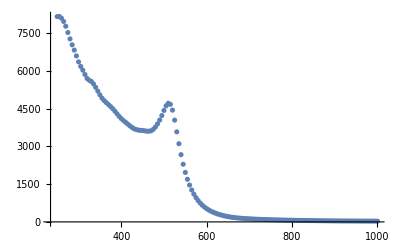

```mathematica
ListPlot[auCextMie]
```

```mathematica
mieQext[nindexau[h c/1.721],1,30,h c/1.721][[3]]
```

104.302

```mathematica
h c/5
```

248.14

```mathematica
upperTicks4=Module[{labels,positions},labels={1.2,1.5,2,3,6};
positions=h c/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={1,1.3,1.7,1.8,2.3,2.7,4,5,5.7};
positions=h c/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

```mathematica
au1=ListLinePlot[{Style[varindep20,RGBColor[1,0.902,0.145]],Style[varindep21,Orange]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Qext, Qsca",Black,12],None},{Style["λ [nm]",Black,12],Style["ℏω [eV]",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicks4,upperTicksMinor4]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",12]&/@{"Qext","Qsca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.8,0.7}]]
```

-Graphics-

# Eritrocitos

```mathematica
(*se van a exportar los datos del ajuste de CST para comparar bien la convergencia*)
```

```mathematica
datosIM=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\Funciones_dielectricas\\CST\\epsEritrocitosData30_Im_Fit.csv"];
datosRE=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\Funciones_dielectricas\\CST\\epsEritrocitosData30_Re_Fit.csv"];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
parteImFit=Interpolation[Transpose[{datosIM[[All,1]],datosIM[[All,2]]}]];
parteReFit=Interpolation[Transpose[{datosRE[[All,1]],datosRE[[All,2]]}]];

nindexEriFit[lambda_]:=Sqrt[parteReFit[lambda]+I*parteImFit[lambda]]
```

```mathematica
eriCabsMieFit=Table[{λ,mieQabs[nindexEriFit[λ],Sqrt[1.82],2680,λ][[3]]},{λ,400,600,5}];
eriCscaMieFit=Table[{λ,mieQsca[nindexEriFit[λ],Sqrt[1.82],2680,λ][[3]]},{λ,400,600,5}];
eriCextMieFit=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.82],2680,λ][[3]]},{λ,400,600,5}];
```

```mathematica
eriCextMieExpInterp=Interpolation[eriCextMieExp];
eriCextMieFitInterp=Interpolation[eriCextMieFit];
```

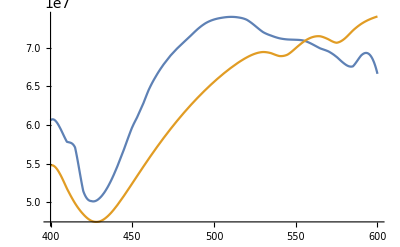

```mathematica
Plot[{eriCextMieExpInterp[x],eriCextMieFitInterp[x]},{x,400,600}]
```

```mathematica
h c/650
```

1.90877

```mathematica
Clear[nindexEri30]
```

```mathematica
nindexEri30[lambda_]:=Sqrt[partere302[h c/lambda]+I*parteim302[h c/lambda]]
nindexPlasma[lambda_]:=Sqrt[parterePlasma2[h c/lambda]]
```

```mathematica
partere302[h c/400]
```

2.00192

```mathematica
Re[nindexEri30[450]]
```

1.42336

```mathematica
Re[nindexPlasma[400]]
nindexPlasma[450]
```

1.35038

1.35038

```mathematica
Plot[Re[nindexEri30[x]],{x,400,800}]
```

```mathematica
0.2418*h c/0.46121916615385
partere302[h c/500]
parteim302[h c/500]
```

650.453

2.03158

0.00281195

```mathematica
eriCabsMie=Table[{0.2418*h c/λ,mieQabs[nindexEri30[λ],nindexPlasma[λ],2680,λ][[3]]},{λ,400,800,5}];
eriCscaMie=Table[{0.2418*h c/λ,mieQsca[nindexEri30[λ],nindexPlasma[λ],2680,λ][[3]]},{λ,400,800,5}];
eriCextMie=Table[{0.2418*h c/λ,mieQext[nindexEri30[λ],nindexPlasma[λ],2680,λ][[3]]},{λ,400,800,5}];
```

```mathematica
eriQabsMie=Table[{0.2418*h c/λ,mieQabs[nindexEri30[λ],nindexPlasma[λ],2680,λ][[4]]},{λ,400,800,5}];
eriQscaMie=Table[{0.2418*h c/λ,mieQsca[nindexEri30[λ],nindexPlasma[λ],2680,λ][[4]]},{λ,400,800,5}];
eriQextMie=Table[{0.2418*h c/λ,mieQext[nindexEri30[λ],nindexPlasma[λ],2680,λ][[4]]},{λ,400,800,5}];
```

```mathematica
Range[400,800,100]
```

{400,500,600,700,800}

```mathematica
parterePlasma2[h c/800]
```

1.82352

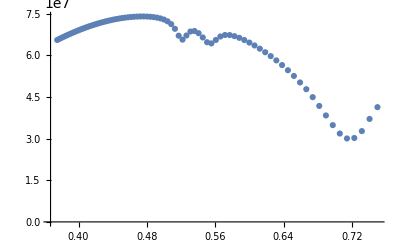

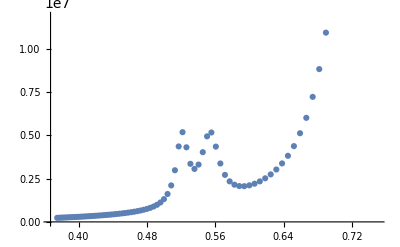

```mathematica
ListPlot[{eriCscaMie}]
ListPlot[{eriCabsMie}]
```

```mathematica
mieQsca[nindexEri30[650],1.33,2680,650][[3]]
mieQabs[nindexEri30[650],1.33,2680,650][[3]]
```

6.94338×10^7

577309.

```mathematica
(Abs[(67986177.865712
-6.943382768591876*^7)]/6.943382768591876*^7)*100
```

2.08493

```mathematica
N[(Abs[(52250-577309)]/577309)*100]
```

90.9494

```mathematica
mieQsca[nindexEri30[650],Sqrt[1.8235],2680,650][[3]]/(Pi*(2680)^2)
mieQabs[nindexEri30[650],Sqrt[1.8235],2680,650][[3]]/(Pi*(2680)^2)
```

3.26941

0.0248442

```mathematica
52047118.005380/(Pi*(2680)^2)
4316542.2128142/(Pi*(2680)^2)
```

```mathematica
mieQsca[nindexEri30[650],Sqrt[1.8235],2680,400][[3]]/(Pi*(2680)^2)
mieQabs[nindexEri30[650],Sqrt[1.8235],2680,400][[3]]/(Pi*(2680)^2)
37145919.777054/(Pi*(2680)^2)
251734.47123326/(Pi*(2680)^2)
```

2.06563

0.0400993

1.64623

0.0111564

```mathematica
100*(609936.64390921
-560589.7804984748)/560589.7804984748
```

8.80267

```mathematica
.8
```

```mathematica
100*(50742522.849344-7.37716458740313*^7)/7.37716458740313*^7
```

-31.2168

```mathematica
100*(553587.12535341-560589.7804984748)/560589.7804984748
100*(74764611.869414-7.37716458740313*^7)/7.37716458740313*^7
```

-1.24916

1.346

```mathematica
hz={0.37474057250000,0.39972327733333,0.42827494000000,0.46121916615385,0.49965409666667,0.54507719636364,0.59958491600000,0.66620546222222,0.74948114500000};
acs={127224.98232573,180749.10209046,291509.41975163,550106.40835717,1494477.2686203,4196398.1531981,1832481.2539712,5958455.9385341,14581298.391387};
rcs={66684640.137611,70376213.651721,73350593.338403,74784394.875777,72713505.529960,65451467.292387,61086234.722512,41696447.009477,38429231.487435};
```

```mathematica
acs2={232726.24938864,290028.12638710,422701.15127936,576448.56629902,1417992.4637892,4311765.3812826,2409890.9565549,6397243.3819210,20828360.61101};
rcs2={37225915.296472,39874800.459289,45811156.805630,53000419.736426,56912393.947055,50426142.398761,43732704.858460,37624377.740598,28726852.720477};
```

```mathematica
acs3={251734.47123326,299302.19086997,428451.36633469,590879.74708138,1406745.1292454,4316542.2128142,2364010.3079086, 6374358.1274467,15444234.051619 };
rcs3={37145919.777054,38682113.294844,43587117.415541,50880332.818491,56101527.297670,52047118.005380,46081609.306600,36138566.003071,31807954.979497};
acs4={138770.75494917,191915.73605719,299963.68347846,553597.98946744,1470759.2743306,4282022.3713201,1821536.0494122,5954407.282395,14588457.365705 };
rcs4={66646919.199664,70341497.913405,73320250.729960,74765528.152960,72752764.377880,65298264.453741,61152652.500001,41742392.815536,38455229.762643};
acs5={134417.12243345,191901.39237951,300776.57182875,552493.16788325,1469293.3716876,4282915.6731356,1823292.3330550,5950602.1663077,14578894.635066};
rcs5={66747640.797514,70439872.755771,73414125.094846,74844268.065330,72789586.511206
,65278391.358947,61012127.478956,41560733.066552,38314506.309517};
```

```mathematica
eriCscaMie3=Table[{0.2418*h c/λ,mieQsca[nindexEri30[λ],Sqrt[1.8235],2680,λ][[3]]},{λ,400,800,50}];
eriCabsMie3=Table[{0.2418*h c/λ,mieQabs[nindexEri30[λ],Sqrt[1.8235],2680,λ][[3]]},{λ,400,800,50}];
eriCscaMie4=Table[{0.2418*h c/λ,mieQsca[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[3]]},{λ,400,800,50}];
eriCabsMie4=Table[{0.2418*h c/λ,mieQabs[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[3]]},{λ,400,800,50}];
```

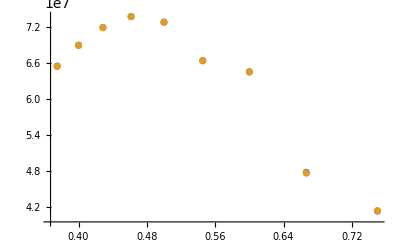

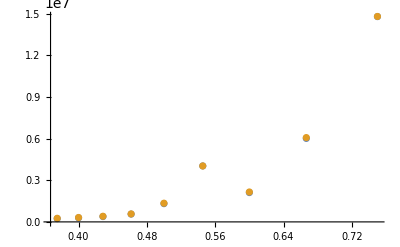

```mathematica
ListPlot[{eriCscaMie3,eriCscaMie4},PlotRange->All]
ListPlot[{eriCabsMie3,eriCabsMie4},PlotRange->All]
```

```mathematica
ListPlot[{Transpose[{hz,acs3}],Transpose[{hz,acs4}],Transpose[{hz,acs5}],eriCabsMie3},PlotRange->All,ScalingFunctions->"Log",PlotLegends->Automatic]
ListPlot[{Transpose[{hz,rcs4}],eriCscaMie3},PlotRange->All,ScalingFunctions->"Log"]
ListPlot[{Transpose[{hz,rcs5}],eriCscaMie4},PlotRange->All,ScalingFunctions->"Log"]
```

```mathematica
100*Abs[(acs4-Sort[eriCabsMie3][[All,2]])]/Sort[eriCabsMie3][[All,2]]
```

{40.9525,34.6083,22.123,1.24722,11.8216,6.27585,13.7922,0.978608,1.33375}

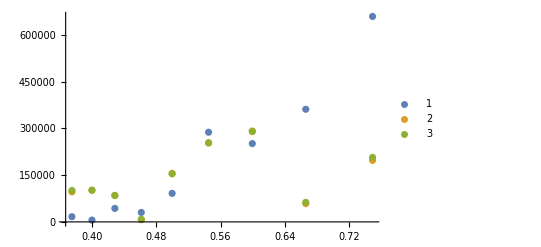

```mathematica
ListPlot[{Transpose[{hz,Abs[(acs3-Sort[eriCabsMie3][[All,2]])]}],Transpose[{hz,Abs[(acs4-Sort[eriCabsMie3][[All,2]])]}],Transpose[{hz,Abs[(acs5-Sort[eriCabsMie3][[All,2]])]}]},PlotRange->All,PlotLegends->Automatic]
```

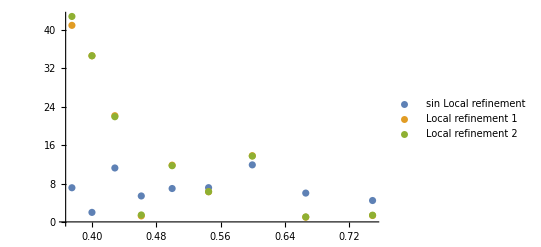

```mathematica
0.2418*h c/0.4
```

750.003

```mathematica
100*Abs[(rcs2-Sort[eriCscaMie3][[All,2]])]/Sort[eriCscaMie3][[All,2]]
```

{43.1596,42.1946,36.3112,28.1561,21.8616,24.0612,32.2463,21.2305,30.4489}

```mathematica
ListPlot[{Transpose[{hz,100*Abs[(rcs3-Sort[eriCscaMie3][[All,2]])]/Sort[eriCscaMie3][[All,2]]}],Transpose[{hz,100*Abs[(rcs4-Sort[eriCscaMie3][[All,2]])]/Sort[eriCscaMie3][[All,2]]}],Transpose[{hz,100*Abs[(rcs5-Sort[eriCscaMie3][[All,2]])]/Sort[eriCscaMie3][[All,2]]}]},PlotRange->All,PlotLegends->Automatic]
```

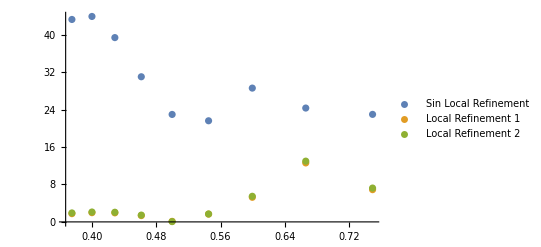

```mathematica
n28ExpAjuste[x_]:=Sqrt[eps28Re[x]+I*fit28tot[x]]
n28lambdaExpAjuste[x_]:=n28ExpAjuste[h c/x]
n28ExpExp[x_]:=parteRe28[x]+I*parteIm28[x]
n28lambdaExpExp[x_]:=n28ExpExp[h c/x]
```

```mathematica
eriQextMieAjuste=Table[{λ,mieQext[n28lambdaExpAjuste[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,400,600,1}];
eriQextMieExp=Table[{λ,mieQext[n28lambdaExpExp[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,400,600,1}];
```

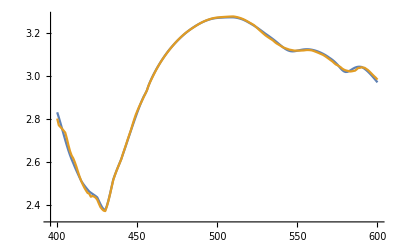

```mathematica
ListLinePlot[{eriQextMieAjuste,eriQextMieExp}]
```

```mathematica
n28Reconstruccion[x_]:=Sqrt[partere282[x]+I*fit28tot[x]]
n28lambdaReconstruccion[x_]:=n28Reconstruccion[h c/x]
```

```mathematica
eriQextMieRecons=Table[{λ,mieQext[n28lambdaReconstruccion[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,400,600,1}];
```

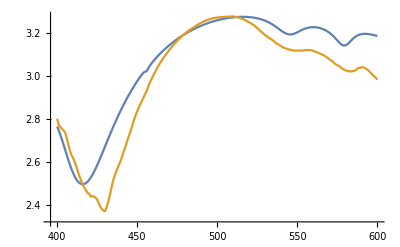

```mathematica
ListLinePlot[{eriQextMieRecons,eriQextMieExp}]
```